Jonas Neundorf, Jan Skottke

# Blatt 2: Quantitatives zur Synchrotonstrahlung

## Vorbetrachtungen

#### Definiere die Konstanten

```mathematica
constants={c->3*10^8,q-> 1.602*10^-19,R->50,ϵ0-> 8.854*10^-12};
```

#### Definiere einige Funktionen

```mathematica
β0[γ_:γ] := Sqrt[1 - 1/γ^2]
```

```mathematica
β[τ_, γ_:γ]:= β0[γ]*{0, Cos[(β0[γ]*c)/(2π*R)*τ],Sin[(β0[γ]*c)/(2π*R)*τ]}
```

```mathematica
βDot[τ_,γ_:γ] := D[β[τ], τ]
```

```mathematica
r[τ_,γ_:γ] := R*{0,Cos[(Norm[β[τ]]*c)/(2π*R)*τ], Sin[(Norm[β[τ]]*c)/(2π*R)*τ]}
```

```mathematica
n[θ_] := {Sin[θ], 0, Cos[θ]}
```

#### Bestimme die verschiedenen Integranden für θ = 0, θ =/= 0 und den Phasenfaktor:

```mathematica
σ[τ_,θ_]=Evaluate[ (Cross[n[θ],Cross[(n[θ]-β[τ]),βDot[τ]]]/(1-β[τ].n[θ])^2)[[2]]//.constants];
```

```mathematica
pi[τ_,θ_]=Evaluate[((Cross[n[θ],Cross[(n[θ]-β[τ]),βDot[τ]]]/(1-β[τ].n[θ])^2)[[1]])^2+((Cross[n[θ],Cross[(n[θ]-β[τ]),βDot[τ]]]/(1-β[τ].n[θ])^2)[[3]])^2//.constants];
```

```mathematica
phase[τ_,θ_,ω_] =Evaluate[Exp[I*ω*(τ-n[θ].r[τ]/c)]//.constants];
```

```mathematica
ωc=3/2*γ^3*c/R//.constants//.γ->6000; (*berechne ωc*)
```

```mathematica
τc=R/(c*γ)//.constants;(*berechne das Zeitintervall τc*)
```

#### Definiere ein Modul um die Strahlungsleistung zu berechnen

```mathematica
d2I[θ_,γ_:γ,n_:2000]:=Module[{σtable,pitable,phasetable,total,integral},

σtable=Table[σ[i, θ],{i,-40*τc,40*τc,((40*τc*2)/n)}];(*berechne die σ-Komponente im Zeiterintervall τc*)
pitable=Table[pi[i,θ],{i,-40*τc,40*τc,((40*τc*2)/n)}];(*berechne die π-Komponente im Zeiterintervall τc*)
phasetable=Table[phase[i,θ,j*ωc],{i,-40*τc,40*τc,((40*τc*2)/n)},{j,0.05,5,0.05}];(*berechne den Phasenfaktor im Zeitintervall τc und zu den verschiedenen Frequenzpunkten ω*)

total=Total[σtable*pitable*phasetable]; 
(*gibt zurück mit den Werten des Integrals. Jeder Eintrag ist ein ω-Wert. Multipliziere den Phasenfaktor mit dem σ- und π-Term und bestime die Summe der einzelnen ω-Werte*)
integral=Evaluate[q^2/(16 π^3*ϵ0*c)*Map[Abs, total*(80*τc)/n]//.constants];(*Berechne das Integral in dem die Schrittweite dazu multipliziert wird. Zurückgegeben wird eine Liste*)
Return[integral]
]
```

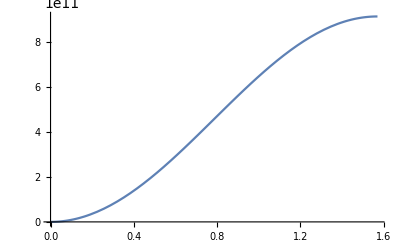

```mathematica
Plot[pi[τc, θ]//.γ->6000,{θ, 0, π/2}]
```

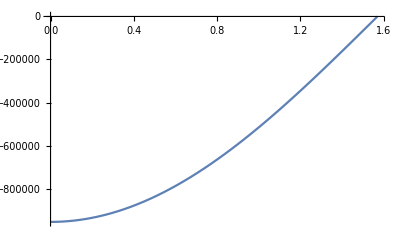

```mathematica
Plot[σ[τc, θ]//.γ->6000, {θ, 0, π/2}]
```